```mathematica
FnIntegrand[n_,x_,λ_,ν_]:=(x^(n/2)(1+λ/2 x))/(Exp[x+λ^-1-ν]+1)
```

```mathematica
neIntegrand[x_,λ_,ν_]:=(FnIntegrand[1,x,λ,ν]+λ FnIntegrand[3,x,λ,ν])
```

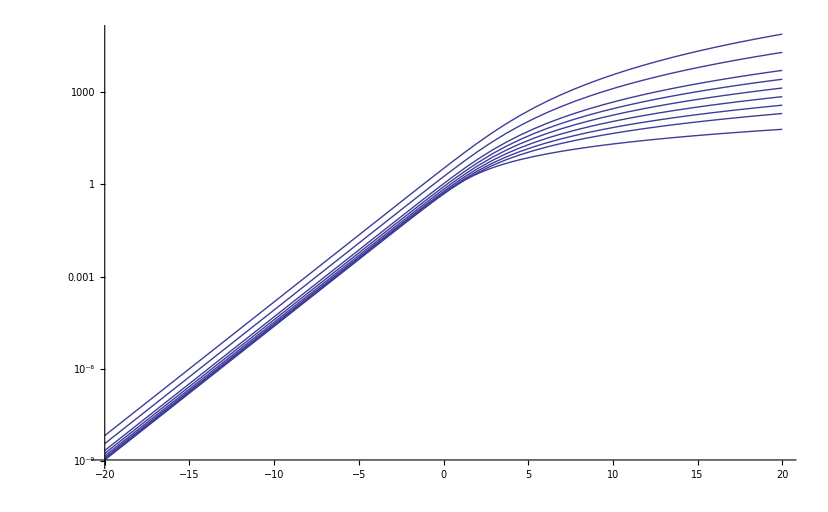

```mathematica
With[{λ=1},LogPlot[Table[NIntegrate[FnIntegrand[n,x,λ,ν],{x,0,∞}],{n,{-1/2,1/2,1,3/2,2,5/2,3,4,5}}],{ν,-20,20}]]
```